# Polar and Parametric Curves With Mathematica

## This notebook will show you some helpful functions for visualizing some introductory concepts from Multivariable Calculus, as well as how to build your own functions for some key equations. This will helpful for students who have a good mathematical foundation and are just starting Multivariable Calculus.

## Parametric Plots

### ParametricPlot takes in a total of 5 arguments: The first two being the x and y functions, The third being the variable they're in terms of (often "t"), And the last two encompass the range of that variable.

```mathematica
ParametricPlotpaclet:ref/ParametricPlot[{Subscript[f, x],Subscript[f, y]},{u,Subscript[u, min],Subscript[u, max]}]
```

```mathematica
Manipulate[ParametricPlot[{Sin[t]+.5*Sin[5*t]+.25*Cos[2.3*t], Cos[t]+.5*Cos[5*t]+.25*Sin[2.3*t]}, {t, 0.001, m}, Mesh->Full,PlotRange->{{-2,2},{-2,2}}], {m,0,100}]
```

#### Here’s a few examples of curves that would be difficult to plot by hand:

```mathematica
Manipulate[ParametricPlot[{Sin[t]+.5*Sin[5*t]+.25*Cos[2.3*t], Cos[t]+.5*Cos[5*t]+.25*Sin[2.3*t]},{t,0,m}], {m, 0, 30}]
```

ParametricPlot::plld: Endpoints for t in {t,0,FE`m$$52} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

ParametricPlot::plld: Endpoints for t in {t,0,FE`m$$50} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

ParametricPlot::plld: Endpoints for t in {t,0,FE`m$$50} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

ParametricPlot::plld: Endpoints for t in {t,0,FE`m$$48} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

```mathematica
Manipulate[ParametricPlot[{r Cos[x],r Sin[x]},{x,1,m},{r,0,k},Mesh->Full,PlotRange->{{-2,2},{-2,2}}],{m,0,5 Pi},{k,1,2}]
```

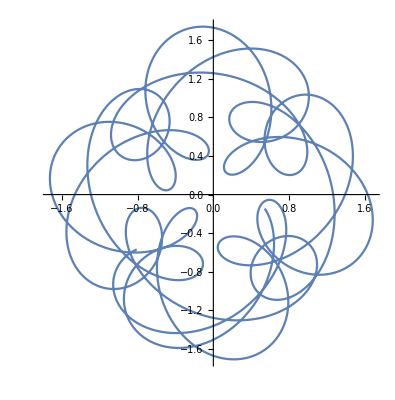

```mathematica
ParametricPlot[{Sin[t]+.5*Sin[5*t]+.25*Cos[2.3*t], Cos[t]+.5*Cos[5*t]+.25*Sin[2.3*t]}, {t, -10, 10}]
```

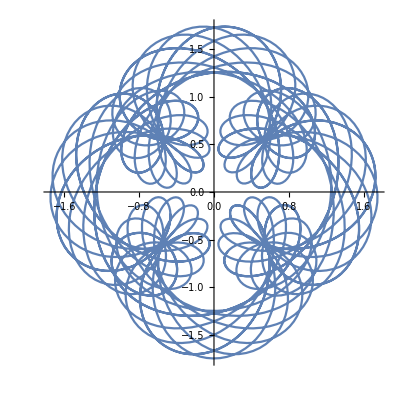

```mathematica
ParametricPlot[{Sin[t]+.5*Sin[5*t]+.25*Cos[2.3*t], Cos[t]+.5*Cos[5*t]+.25*Sin[2.3*t]}, {t, -40, 40}]
```

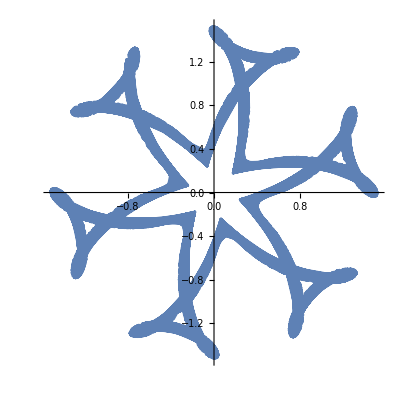

```mathematica
ParametricPlot[{Sin[t]+.5Cos[5t]+.25Sin[13t], Cos[t]+.5Sin[5t]+.25Cos[13t]}, {t, -250, 250}]
```

## Polar Curves and Plotting Techniques

```mathematica
Plotpaclet:ref/Plot[f,{x,Subscript[x, min],Subscript[x, max]}]
```

#### The first input f is the function you're using, followed by a list: {function variable, min range, and max range}

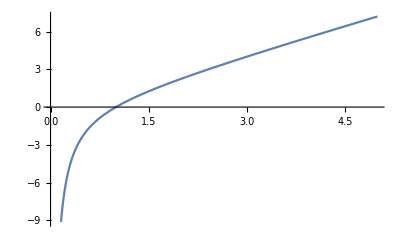

```mathematica
Plot[(-3+3 x^2)/(2 x), {x, 0, 5}]
```

#### You can put multiple plots simply with the following format

```mathematica
Plotpaclet:ref/Plot[{Subscript[f, 1],Subscript[f, 2],…},{x,Subscript[x, min],Subscript[x, max]}]
```

#### For PolarPlot, the inputs are different. We need a [radius, {function variable, min range, max range}]

```mathematica
PolarPlotpaclet:ref/PolarPlot[r,{θ,Subscript[θ, min],Subscript[θ, max]}]
```

#### If you plug in a number for the radius, it remains constant for that number as the angle rotates around the circle:

```mathematica
PolarPlot[2, {t, 0, 2Pi}]
```

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$83} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$83} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$83} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$27} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$81} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$81} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$81} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$29} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$27} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$79} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$79} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$79} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$79} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$31} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$29} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$77} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

PolarPlot::plld: Endpoints for t in {t,0,FE`m$$75} must have distinct machine-precision numerical values.

General::stop: Further output of PolarPlot::plld will be suppressed during this calculation.

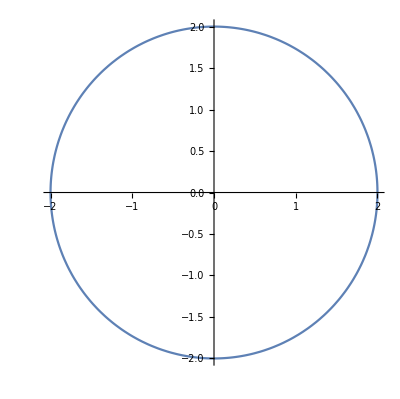

```mathematica
Manipulate[PolarPlot[t, {t, 0, m}, PlotRange->{{-10Pi, 10Pi}, {-10Pi, 10Pi}}], {m, 0.001, 100Pi}]
```

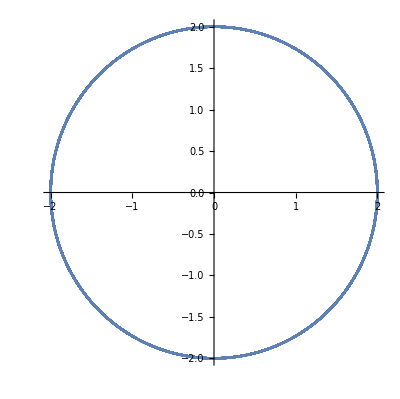

```mathematica
PolarPlot[2, {t, 0, 100Pi}]
```

#### However, if you input the variable instead of a constant, the radius will start at the angle range you specify and increase with the range. This is useful because it actually shows how many rotations occur around the circle with the given ranges:

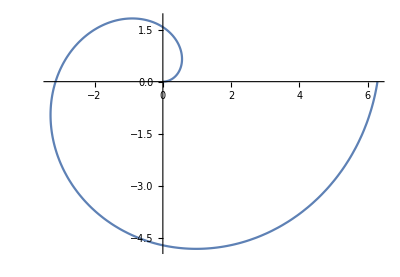

```mathematica
PolarPlot[t, {t, 0, 2Pi}]
```

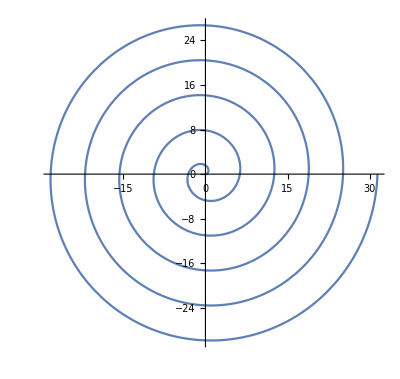

```mathematica
PolarPlot[t, {t, 0, 10Pi}]
```

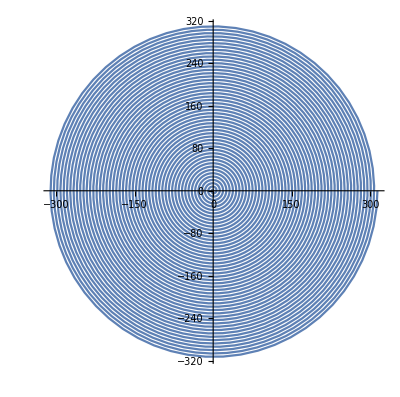

```mathematica
PolarPlot[t, {t, 0, 100Pi}]
```

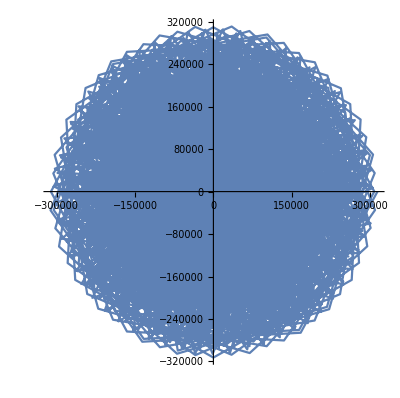

```mathematica
PolarPlot[t, {t, 0, 100000Pi}]
```

#### Comparing these two types of plots is often helpful for people first learning the way parametric curves trace. Building a function that outputs both forms of a curve is easy to do :

```mathematica
polarAndCartesian[f_, var_, a_, b_] := 

{Plot[f, {var,a,b}, ImageSize -> 400,Ticks->{{0, Pi/4,Pi/2,3Pi/4,Pi,5Pi/4,3Pi/2,7Pi/4, 2Pi},{-1,1}}], 
PolarPlot[f, {var, a, b} ,ImageSize -> 400]}
```

#### This function accepts another function ( f ), what variable the functions are in terms of ( var ), and the range ( a, b ) to output both plot forms. The tick marks have also been specified to go in increments of Pi/4 for the Cartesian graph:

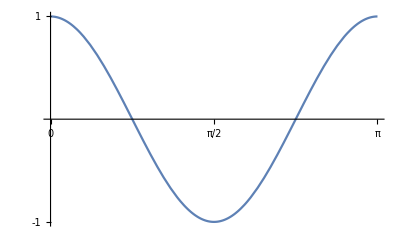
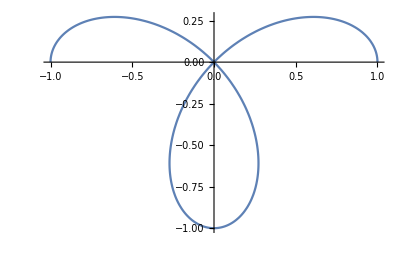

```mathematica
polarAndCartesian[Cos[2Theta], Theta, 0, Pi]
```

#### Finally for this section, there exists two handy tools to easily convert from polar to Cartesian or vice versa, FromPolarCoordinates and ToPolarCoordinates:

```mathematica
ToPolarCoordinates[{1, -1}]
```

{√2,-π/4}

```mathematica
FromPolarCoordinates[{Sqrt[2],-Pi/4}]
```

{1,-1}

## Building Functions with Derivatives and Integrals

#### To differentiate a function, simply type D[f, x], where f is the function and x is the term the function is in. To specify 2nd, 3rd, or nth derivative, write D[f, {x, n}], where variables are the same as the previous D function, except you can specify up to the nth derivative.

```mathematica
D[f,x]  

D[f, {x, n}]
```

```mathematica
D[Cos[2x]+4x^5, x]
```

20 x^4-2 Sin[2 x]

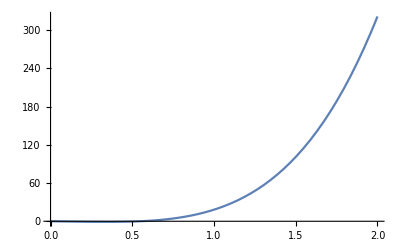

```mathematica
Plot[20 x^4-2 Sin[2 x], {x, 0, 2}]
```

```mathematica
D[Cos[2x]+4x^5, x, {x, 4}]
```

480-32 Sin[2 x]

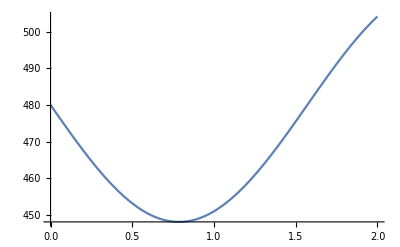

```mathematica
480-32 Sin[2 x]

Plot[480-32 Sin[2 x], {x, 0, 2}]
```

```mathematica
D[Cos[2u]+4u^5,{u, 3}]
```

240 u^2+8 Sin[2 u]

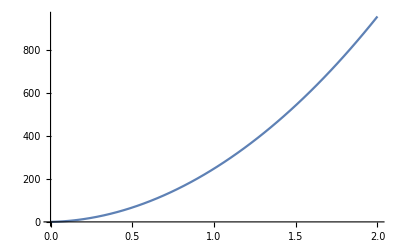

```mathematica
Plot[240 u^2+8 Sin[2 u], {u, 0, 2}]
```

#### Integration works similarly, with the function being Integrate[f, x], which gives the indefinite integral of the function. Providing Integrate[f, {x, x-min, x-max}] give you a definite integral of a function through a certain range.

```mathematica
Integrate[4x^2 + 6Sin[3x]-(12x^2/x^2), x]
```

```mathematica
-12 x+(4 x^3)/3-2 Cos[3 x]
```

```mathematica
Integrate[4x^2 + 6Sin[3x]-(12x^2/x^2),{ x, 0, 4}]
```

112/3+4 Sin[6]^2

#### You can also directly create integral and derivate symbols via pressing the esc button. The integration symbol is made by first pressing “esc” key, followed by typing “int”, then pressing “esc” again. For derivative, you press “esc”, typing “dd” then hit “esc” again:

```mathematica
∫(Cos[2x]+Sin[2x])ⅆx
```

-1/2 Cos[2 x]+1/2 Sin[2 x]

#### You can also set upper and lower limits once the integration symbol is made by typing ctrl_ for the lower limit and ctrl% for the upper limit:

```mathematica
∫_0^5 (Cos[2x]+Sin[2x])ⅆx
```

Sin[5] (Cos[5]+Sin[5])

#### You can combine the Derivative and Integration function to make useful functions that will compute key equations from preliminary multivariable calculus. The one below is the equation to find the slope of the tangent of a parametric curve:

### -Graphics-

```mathematica
derivOfParaTangent[x_,y_, var_]:=( D[y, var])/(D[x, var])
```

```mathematica
derivOfParaTangent[18(t)^2, 4ln(t), t]
```

ln/(9 t)

#### Another is a function to easily compute the length of the tangent line:

#### -Graphics-

```mathematica
lengthOfTangent[x_, y_, var_, a_, b_] := Integrate[Sqrt[(D[x])^2+(D[y])^2], {var, a, b}]
```

```mathematica
lengthOfTangent[2(x^2)-10x, 4(x), x, 0, 5]
```

```mathematica
1/3 (16+17 √29+60 ArcSinh[5/2])
```

```mathematica
lengthOfTangent[12x^2-2x, 10(x), x, 0, 5]
```

1/108 (-49 √26+1819 √866+75 ArcSinh[29/5]+75 Log[5]-75 Log[-1+√26])

## Questions to try:

1) Take the 5th derivative of 12x^7+ (7x)/3  and then plot it from 0 to 8


2) Make a polar plot that that will travel completely around the coordinate plane 1000 times


3) Aside from the functions posted here utilizing integration and derivation to form useful equations, what are some other
equations from calculus that could be created using the tools given here?


4) Use the integral and derivative symbols  to take the double integral of Sin[xy], where the inner integral symbol is
from 0 to x and the outer integral is from 0 to 1, in terms of dy and dx